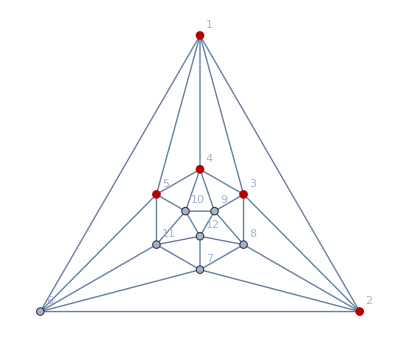

```mathematica
Graph[Graph[plantri[[1]]],VertexLabels->"Name", GraphHighlight->{1,2,3,4,5}, GraphLayout->"TutteEmbedding"]
```

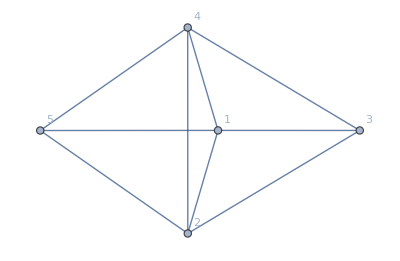

```mathematica
Subgraph[MinimalGraph2[8],{1,2,3,4,5},VertexLabels->"Name"]
```

```mathematica
FindFullFormula1234[Subgraph[MinimalGraph2[8],{6,9,1,2},VertexLabels->"Name"]]
```

{v1x2x6x9,v1x29x6,v19x2x6,v16x2x9,v16x29,v1x2x69,v169x2}

```mathematica
GraphSignature2[MinimalGraph2[8]]
```

7-7-5-5-4-4-4-3-3

```mathematica
85+1+86
```

172

```mathematica
171*2
```

342

```mathematica
With[
{master=Graph[plantri[[1]]]},Map[With[{g=EmbedSymbolInGraph[master,#]},Labeled[g,{#,SymbolToLabel[#],PlanarGraphQ[g],ChromaticPolynomial[g,4]/24,FindClique[g]}]]&,Sort[FindFullFormula1234[Subgraph[master,{4,5,9,12,11},VertexLabels->"Name"]],CompareSymbols]]
]
```

{-Graphics-{v4x5x9bxc,4♁5♁9b♁c,False,0,{{4,5,9,10,12}}},-Graphics-{v4x5cx9xb,4♁5c♁9♁b,False,0,{{4,5,9,10,11}}},-Graphics-{v4x5cx9b,4♁5c♁9b,False,2,{{5,6,7,9}}},-Graphics-{v4x59xbxc,4♁59♁b♁c,False,0,{{4,5,10,11,12}}},-Graphics-{v4bx5x9xc,4b♁5♁9♁c,False,0,{{4,5,9,10,12}}},-Graphics-{v4bx5cx9,4b♁5c♁9,False,2,{{1,4,5,6}}},-Graphics-{v4bx59xc,4b♁59♁c,False,2,{{1,3,4,5}}},-Graphics-{v4cx5x9xb,4c♁5♁9♁b,False,0,{{4,5,9,10,11}}},-Graphics-{v4cx5x9b,4c♁5♁9b,False,2,{{3,4,8,9}}},-Graphics-{v4cx59xb,4c♁59♁b,False,2,{{3,4,5,8}}}}